# Mathematica Guidebook, Programming

```mathematica
DateString[]
```

Thu 3 Dec 2015 17:22:14

```mathematica
Sin[Pi/3]//N
```

0.866025

```mathematica
int1=111111^222222
```

16770945117885810986884156054743539021856023975990858768807270862401611985048893479079773293821109221442469464482013448104798003528463384474603334906454189258149266954774096873815018121270112090340073581950458335785895046332658797258921624716998798353756214738640362255508441294027934894073849730952870477394740281371186875383147131163055565685154042950701084798657190619462615421521
 |  |  |  |

```mathematica
int2=222222^333333
```

37015273992922194974120909785944692495352640320749915975100329227176724379957900336032187606120071184745850975073180200812581573186959296369291648465794594084919695691420482302446531392182178188574608090085562087782251090514090176572658802366747201622025574278659598728332257360417601798011395489537064334299658470523582666279561306798835797695230115320861594836343624930222147633152
 |  |  |  |

```mathematica
Timing[int3=int1 int2;]
```

{0.032,Null}

```mathematica
Do[1,{10^8}]//Timing
```

{1.132,Null}

```mathematica
NIntegrate[x^3,{x,0,1}]
```

0.25

```mathematica
f = Sin[Log[Tan[(ζ^2+Exp[x])/(Cos[ζ^2-1]+Sqrt[ζ])]]]
```

Sin[Log[Tan[(ⅇ^x+ζ^2)/(√ζ+Cos[1-ζ^2])]]]

```mathematica
D[f,{ζ,2}]//Short[#,4]&
```

-Cos[Log[Tan[(ⅇ^x+ζ^2)/(√ζ+Cos[1-ζ^2])]]] Csc[(ⅇ^x+ζ^2)/(√ζ+Cos[1-ζ^2])]^2 ((2 ζ)/(√ζ+Cos[1-ζ^2])-((ⅇ^x+ζ^2) (1/(2«1»«1»)+«1»))/(√ζ+«1»)^2)^2+«1»+«1»-Csc[(ⅇ^x+ζ^2)/(√ζ+Cos[1-«1»])]^2 Sec[(«1»)/(«1»)]^2 («1»-«1»)^2 Sin[Log[Tan[(ⅇ^x+ζ^2)/(√ζ+Cos[1-ζ^2])]]]

```mathematica
Integrate[Sin[x],x]
```

-Cos[x]

```mathematica
Integrate[1/(x^4+4)^2,{x,-∞,∞}]
```

(3 π)/64

```mathematica
Integrate[Sin[x^2],x,x,x,x,x]
```

1/192 (4 x^3 Cos[x^2]+12 √(2 π) x^2 FresnelC[√(2/π) x]+√(2 π) (-3+4 x^4) FresnelS[√(2/π) x]-10 x Sin[x^2])

```mathematica
DSolve[x''[t]+γ x'[t]+ω^2 x[t]==0,x[t],t]
```

{{x[t]→ⅇ^(1/2 t (-γ-√(γ^2-4 ω^2))) C[1]+ⅇ^(1/2 t (-γ+√(γ^2-4 ω^2))) C[2]}}

```mathematica
Solve[{x^2+y^2==1,x^4+y^4==4},{x,y}]
```

{{x→-ⅈ √(1/2 (-1+√7)),y→-√(1/2 (1+√7))},{x→-ⅈ √(1/2 (-1+√7)),y→√(1/2 (1+√7))},{x→ⅈ √(1/2 (-1+√7)),y→-√(1/2 (1+√7))},{x→ⅈ √(1/2 (-1+√7)),y→√(1/2 (1+√7))},{x→-√(1/2 (1+√7)),y→-ⅈ √(1/2 (-1+√7))},{x→-√(1/2 (1+√7)),y→ⅈ √(1/2 (-1+√7))},{x→√(1/2 (1+√7)),y→-ⅈ √(1/2 (-1+√7))},{x→√(1/2 (1+√7)),y→ⅈ √(1/2 (-1+√7))}}

# Chapter 2, Structure of Mathematica Expressions & Chapter 3, Definitions and Properties of Functions

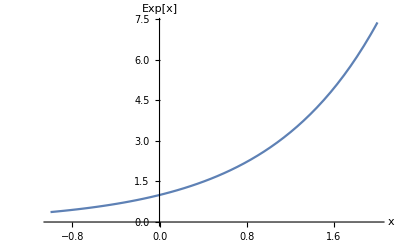

```mathematica
Plot[Exp[x],{x,-1,2},AxesLabel-> {"x","Exp[x]"},PlotStyle->Thick[0.01]]
```

```mathematica
Plot3D[Re[Exp[1/(x+I y)]],{x,-2.001,2},{y,-2.001,2},PlotPoints->60]
```

-Graphics3D-

```mathematica
Sqrt[u^2]
```

√(u^2)

```mathematica
Simplify[Sqrt[u] Sqrt[v],Assumptions->{u>0,v>0}]
```

√(u v)

```mathematica
Options[Plot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotLegends→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PlotTheme:>$PlotTheme,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,TargetUnits→Automatic,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}